In the limit ρ → 0 we assume ψ(i,a) = √(λ_(i',a'))ψ(i’,a’) where i’ and a’ are the renormalized indices afetr a decimation.

The goal of this Mathematica script is to test numerically whether such a scaling matrix λ_(i',a') exists, and to measure it.

```mathematica
(* Fibonacci Hamiltonian, in the co-basis, with periodic bc *)
hp[n_,tw_,ts_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->tw,{i,1,F1}];
tbls=Table[{i,i+F1}->ts,{i,1,F0}];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* wavefunctions in the co-basis, ordered by IDoS label *)
wf=Block[{val,vec,i=9,ts=10.,tw=1.},
{val,vec}=Eigensystem[hp[i,tw,ts]];
(*order wavefunctions by increasing energy*)
vec[[Ordering[val]]]
];
```

When ρ → 0, we see that the intensity on each of the 4 squares of size F_(n-2)×F_(n-2) is the same (perhaps up to a reflection). So, indeed, the intensity on each one of the 4 squares write I(i,a) = λ_(i',a') I(i’,a’), where I(i’,a’) is the intensity at step n-2.

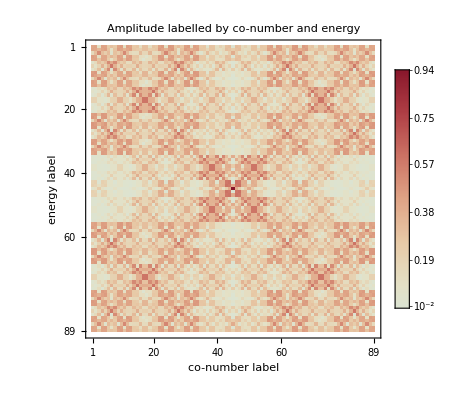

```mathematica
MatrixPlot [Abs[wf]^2,FrameLabel->{"energy label","co-number label"},PlotLabel->"Amplitude labelled by co-number and energy",PlotLegends->Automatic,ColorFunction->"ThermometerColors"]
```

Measuring λ_(i',a')

```mathematica
(* system size *)
n=9;
nd=n-2;
(* coupling *)
ρ=1./8;

(* wavefunctions in the co-basis, ordered by IDoS label *)
wf=Block[{val,vec},
{val,vec}=Eigensystem[hp[n,ρ,1.]];
vec[[Ordering[val]]]
];
(* deflated wavefunctions *)
wfd=Block[{val,vec},
{val,vec}=Eigensystem[hp[nd,ρ,1.]];
vec[[Ordering[val]]]
];
```

```mathematica
(* crop the square [1,Subscript[F, n-2]]×[1,Subscript[F, n-2]] *)
wfcropped=wf[[1;;Fibonacci[n],1;;Fibonacci[n]]];

(* crop the 3 remaining squares *)
(*wfcropped=wf[[1;;Fibonacci[n],Fibonacci[n+1]+1;;Fibonacci[n+2]]];
wfcropped=wf[[Fibonacci[n+1]+1;;Fibonacci[n+2],1;;Fibonacci[n]]];
wfcropped=wf[[Fibonacci[n+1]+1;;Fibonacci[n+2],Fibonacci[n+1]+1;;Fibonacci[n+2]]];*)
```

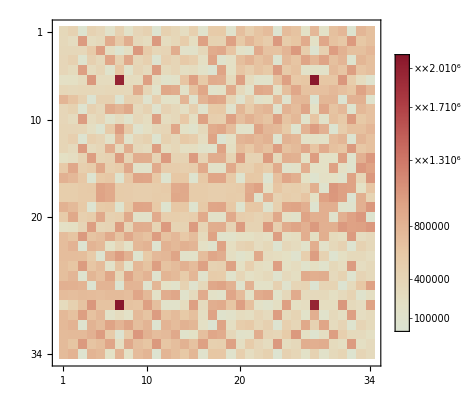

```mathematica
(* λ matrix *)
MatrixPlot[Abs[wfcropped/wfd]^2,ColorFunction->"ThermometerColors",PlotLegends->Automatic]
```

```mathematica
n=9;

(* generate tree *)
t=tree[n];
(* drop site labels *)
t=Transpose[t][[2]];
(* positions of the most molecular sites/clusters *)
idmol=Flatten[Position[t,IntegerPart[n/2]/n]];

(* positions of the most atomic sites/clusters *)
idat=Flatten[Position[t,0]]~Join~Flatten[Position[t,1/n]];
```

```mathematica
(* vector set to 1 at most molecular sites, 0 elsewhere *)
mask=Table[0,{it,Fibonacci[n]}];
mask[[idmol]]=1;
(* tensor product *)
maskmat=Table[mask[[i]]mask[[j]],{i,Fibonacci[n]},{j,Fibonacci[n]}];

mask=Table[0,{it,Fibonacci[n]}];
mask[[idat]]=1;
(* tensor product *)
maskat=Table[mask[[i]]mask[[j]],{i,Fibonacci[n]},{j,Fibonacci[n]}];

mask=-maskat+maskmat;
```

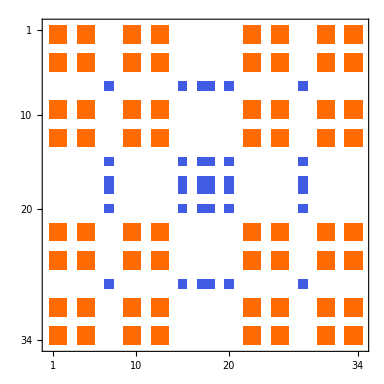

```mathematica
MatrixPlot[mask]
```

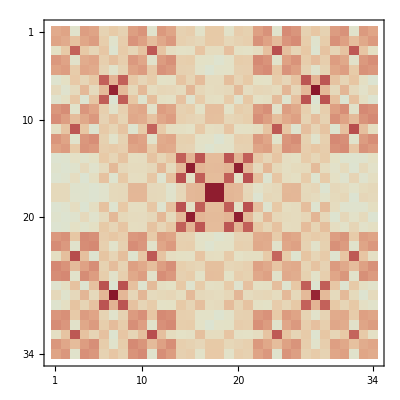

```mathematica
MatrixPlot [Abs[wfcropped]^2,ColorFunction->"ThermometerColors"]
```

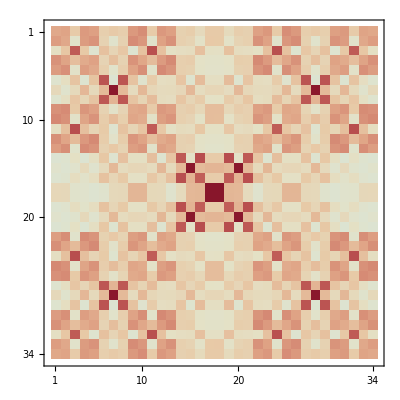

```mathematica
MatrixPlot [Abs[wfd]^2,ColorFunction->"ThermometerColors"]
```

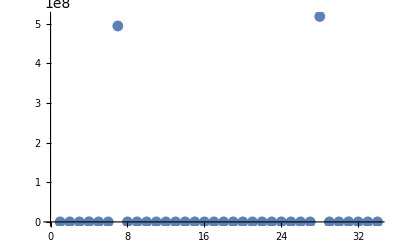

```mathematica
ListPlot[(Abs[wfcropped/wfd]^2)[[Fibonacci[n-3]-2]],PlotRange->All]
```

```mathematica
wfcropped[[Fibonacci[n-2],Fibonacci[n-2]]]
```

0.158362

```mathematica
wfd[[Fibonacci[n-2],Fibonacci[n-2]]]
```

-0.229879

```mathematica
mid=IntegerPart[Fibonacci[n]/2];
c=(wfcropped[[mid,mid]]/wfd[[mid,mid]])^2
```

0.495087

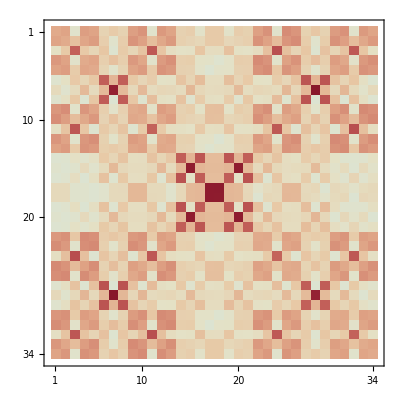

```mathematica
MatrixPlot [Abs[wfcropped]^2,ColorFunction->"ThermometerColors"]
```

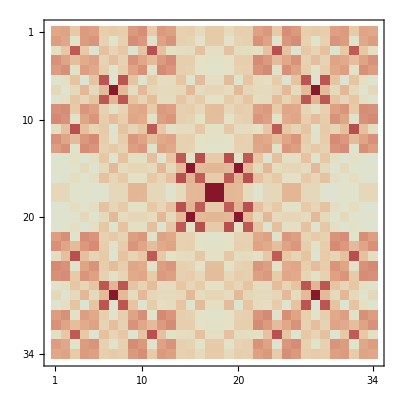

```mathematica
MatrixPlot [Abs[wfd]^2,ColorFunction->"ThermometerColors"]
```